```mathematica
Get["D:\\Schrage.dat"]
```

{0.000759,0.759165,0.293716,0.489063,0.678422,0.239041,0.563328,0.849878,0.891751,0.665211,0.199702,0.383388,49976,0.163371,0.768892,0.773578,0.530645,0.554241,0.135703,0.759254,0.780022,0.830409,0.68516,0.485595,0.389385}
 |  |  |  |

```mathematica
a[[1]]
```

0.000783

```mathematica
data2=Table[{f[[i]],f[[i+1]]},{i,1,50000-1}]
```

{{0.000759,0.759165},{0.759165,0.293716},{0.293716,0.489063},{0.489063,0.678422},{0.678422,0.239041},49989,{0.759254,0.780022},{0.780022,0.830409},{0.830409,0.68516},{0.68516,0.485595},{0.485595,0.389385}}
 |  |  |  |

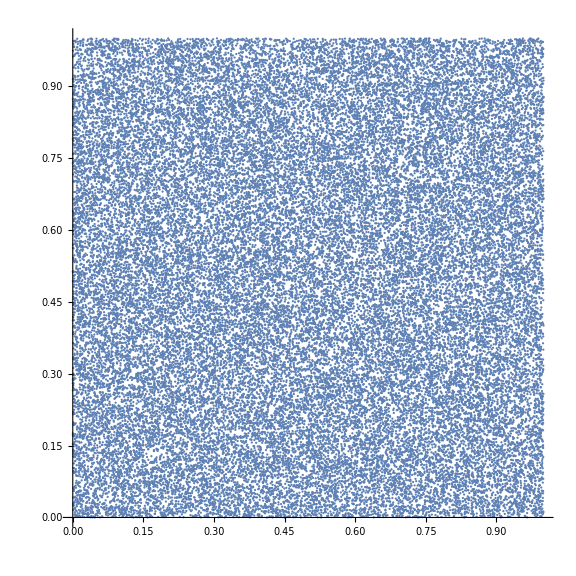

```mathematica
ListPlot[data2,AspectRatio->1,ImageSize->Large]
```

```mathematica
data2[[99999]]
```

{1552075419/2147483647,247707024/2147483647}

```mathematica
f[[1]]
```

1630258